## Set up Environments

```mathematica
Clear["Global`*"]

(*If[$OperatingSystem ==="MacOSX",*)

(*LocalSetting*)
Print["Working in local machine"];
dataDir = "/Users/fish/GoogleDrive/Research/SymBoost/Data";
Import["https://qtechtheory.org/questlink.m"];
CreateDownloadedQuESTEnv[];


(*RemoteSetting*)
(* To run remotely:    wolframscript -file CombMitigation.m&   *)
(*Print["Working in remote machine"];
dataDir = "/home/linc4300/SymBoost/Data";
Import["/questlink/link.m"];
(*CreateLocalQuESTEnv["/questlink/serial"];
CreateLocalQuESTEnv["/questlink/multi"];*)
CreateLocalQuESTEnv["/questlink/gpu"]*)

SetDirectory[dataDir];


On[Assert]
$AssertFunction:=((*1*)SelectionMove[EvaluationNotebook[],All,Notebook,AutoScroll->False];
FrontEndExecute@FrontEndToken@"RemoveFromEvaluationQueue";
SelectionMove[EvaluationCell[],After,Cell,AutoScroll->False];
(*2*)RunScheduledTask[$Pre=.,{1}];
$Pre=Abort[]&;Abort[];);
```

Working in local machine

```mathematica
SinglePauliProd[A_,B_]:=Switch[{A,B},
{X,X},1,    {Y,Y},1,       {Z,Z},1,    
{X,Y},I Z, {Y,X},-I Z,
{Z,X},I Y, {X,Z},-I Y, 
{Y,Z},I X, {Z,Y},-I X ,
_, A*B];

PauliStringToPauliList[pauliString_]:=
Module[{numericalFactor,factorList,indexList,opList ,nQubit,pauliList},
	(*The result is a list of length nqubit + 1, with the first entry being the numerical factor, and entry i is the pauli operator on qubit i - 2*)
	factorList = Flatten[{pauliString/.Times->List}];
	numericalFactor = 1; 
	If[NumericQ[factorList[[1]]], numericalFactor = factorList[[1]]; factorList = factorList[[2;;]]];
	indexList = Table[P/.Subscript[_,a_]:>a,{P,factorList}];
	opList = Table[P/.Subscript[a_,_]:>a,{P,factorList}];
	nQubit = Max[indexList] + 1;
	pauliList = ConstantArray[1,nQubit];
	Do[pauliList[[indexList[[i]]+1]]=opList[[i]],{i,Length[opList]}];
	Join[{numericalFactor}, pauliList]
];

PauliListToPauliString[pauliList_] :=Apply[Times,Table[pauliList[[i]]/.{X->Subscript[X, i-2],Y->Subscript[Y, i-2],Z->Subscript[Z, i-2]},{i,Length[pauliList]}]];

PauliProd[A_,B_]:=
Module[{AList,BList,nQubitA, nQubitB},
	AList = PauliStringToPauliList[A];
	BList = PauliStringToPauliList[B];
	nQubitA = Length[AList]-1;
	nQubitB = Length[BList]-1;
	If[nQubitA≥nQubitB,
		BList = Join[BList, ConstantArray[1,nQubitA - nQubitB]],
		AList = Join[AList, ConstantArray[1,nQubitB - nQubitA]]
	];
	PauliListToPauliString[Table[SinglePauliProd[AList[[i]],BList[[i]]],{i,Length[AList]}]]
]
```

## Initialization

### Input Parameters

```mathematica
nsites = 6; (* nsites takes the value from 4 to 9. From 4 to 6, we have two columns. From 7 to 9 we have 3 columns*)
noiseName = "Bit";
circErrRateList = Range[0.1,0.5,0.1];
paramLabelList={1};
energyThreshold = 0;
writeTimeInterval = 10;

If [Length[$ScriptCommandLine]≠0,
argv=Rest[$ScriptCommandLine];
Scan[ToExpression,argv]];
(* We can overwrite the previous parameters by passing arguments in the commandline like this
"wolframscript -script myScript.m nrows=1 ncols=2"
Note that the arguments are delimit by blankspace, hence we must not have space within the same command.
*)
hopStrength= 1;
repStrength = 2;
nblocks = nsites;
nelectrons = nsites;

Assert[4≤ nsites≤9, "the number of sites in not within the designated range"];
If[nsites ≤6, ncols = 2,ncols = 3];
nrows = Ceiling[nsites /ncols];
```

### Build Folder Structures

```mathematica
mainFolderName="ns-"<>ToString[nsites]<>"_nblk-"<>ToString[nblocks]<>"_ne-"<>ToString[nelectrons];
mainDir = FileNameJoin[{dataDir,mainFolderName}];
Quiet[CreateDirectory[mainDir]CreateDirectory::filex];
SetDirectory[mainDir];
Print["Working in the directory ", mainDir]

(*nParams = (3nsites - 2 + (nrows - 1) * (2 * ncols - 2) ) * nblocks;*)
nParams = (2nsites - 1 + (nrows - 1) * (ncols - 1) ) * nblocks;
paramsSymbolList = Table[Subscript[θ, n],{n,0, nParams- 1}];

nfswap = (2nsites - nrows) * 2 * ncols * nblocks;
nComponents = (nParams -nsites*nblocks)*2 + nsites *nblocks+ nfswap;
```

Working in the directory /Users/fish/GoogleDrive/Research/SymBoost/Data/ns-6_nblk-6_ne-6

### Build Qubit Layout

```mathematica
nqubits = nsites * 2;
sitePairs= Table[{i, i+1},{i,Range[0, nqubits - 1, 2]} ];
(*nsites of them. sitePairs count all Rep pairs*)
spinPairs = Table[{i, i+1},{i,Range[1, nqubits - 2, 2] }];
(*nsites - 1 of them. spinPairs count all Hop Pairs that are ADJACENT to each other in the canonical ordering*)
edgePairs = Table[{i, i+1},{i,Range[2 * ncols - 1, nqubits - 2, 2*ncols]}];
(*nrows - 1 of them. edgePairs count VerHop pairs that are adjacent to each other in the canonical ordering*)
spinNoEdgePairs = Complement[spinPairs,edgePairs];
(*nsites - nrows of them. spinNoEdgePairs count HorHop pairs that are adjacent to each other in the canonical ordering*)
horHopPairs =Join[ Table[{i[[1]]-1, i[[2]]+1}, {i, spinNoEdgePairs}], spinNoEdgePairs];
verHopPairs= Join[Flatten[Table[{i[[1]]-j, i[[2]]+j}, {i, edgePairs[[;;-2]]},{j, 1, 2ncols - 1}],1],edgePairs];
verHopPairs= Join[Table[{edgePairs[[-1,1]]-j, edgePairs[[-1,2]]+j}, {j, 1, 2*Mod[nsites,ncols]-1}],verHopPairs];
spinUpIndex = Select[Range[0,nqubits-1], Mod[#,4]==0 ||Mod[#,4]==3 & ];
spinDnIndex = Select[Range[0,nqubits-1], Mod[#,4]==1 ||Mod[#,4]==2 & ];
```

### Build Hamiltonian Terms

```mathematica
Subscript[hRep, a_,b_]:= (-Subscript[Z, a] - Subscript[Z, b]+ Subscript[Z, a] Subscript[Z, b])/4;
Subscript[hHop, a_,b_]:=(Subscript[X, a] Subscript[X, b] + Subscript[Y, a] Subscript[Y, b])/2 *Apply[Times,Table[Subscript[Z, i],{i,a+1,b-1}]];
hTot = Total[Join[repStrength * Table[Subscript[hRep, i[[1]], i[[2]]], {i, sitePairs}],
					-hopStrength * Table[Subscript[hHop, i[[1]], i[[2]]], {i, horHopPairs}], 
					 -hopStrength * Table[Subscript[hHop, i[[1]], i[[2]]], {i, verHopPairs}]]];
pauliTerms = Table[FactorTermsList[i],{i, Level[hTot//Expand,1]}];
pauliTerms = SortBy[pauliTerms,{StringLength[ToString[#[[2]]]]&,#[[2]]& }];
pauliCoeffList = Table[i[[1]], {i, pauliTerms}];
pauliOpList = Table[i[[2]], {i, pauliTerms}];
pauliOpToString := StringRiffle[Table[StringReplace[i, RegularExpression["[\\[\\] ,]"]->""],{i, StringCases[TextString[#],RegularExpression["\\[[XYZ],[ 0-9]+\\]"]]}]]& ;
pauliNameList = Table[pauliOpToString[i], {i, pauliOpList}];

correctOutcomeList = {Mod[Ceiling[nelectrons/2],2],Mod[ Floor[nelectrons/2],2], Mod[nelectrons,2]};
correctParList = Table[(-1)^outcome,{outcome, correctOutcomeList}];
Print["The correct symmetry eigenvalues are", correctParList];

symNameList = {"Up", "Dn", "Tot"};
symOpIndexList = {spinUpIndex,spinDnIndex,Range[0,nqubits-1]};
symOpList = Table[Product[Subscript[Z, a],{a,symOpIndex}],{symOpIndex,symOpIndexList}] * correctParList;
symMeasTransformList =Table[ Table[Subscript[C, symOpIndex[[i]]][Subscript[X, symOpIndex[[1]]]],{i,2,Length[symOpIndex]}],{symOpIndex,symOpIndexList}];
symMeasGateList = Table[Join[symMeasTransformList[[i]],{Subscript[P, symOpIndexList[[i]][[1]]][correctOutcomeList[[i]]]},Reverse[symMeasTransformList[[i]]]] ,{i,Length[symOpIndexList]}];

coeffFileName = "coeffList.csv";
If[Not[FileExistsQ[coeffFileName]], 
	coeffFile=OpenWrite[coeffFileName];
	WriteString[coeffFile,ExportString[{pauliNameList,pauliCoeffList},"CSV"]];
	Close[coeffFile]
];
```

The correct symmetry eigenvalues are{-1,-1,1}

```mathematica
Total[Abs[pauliCoeffList]]
```

20

### Building Circuit

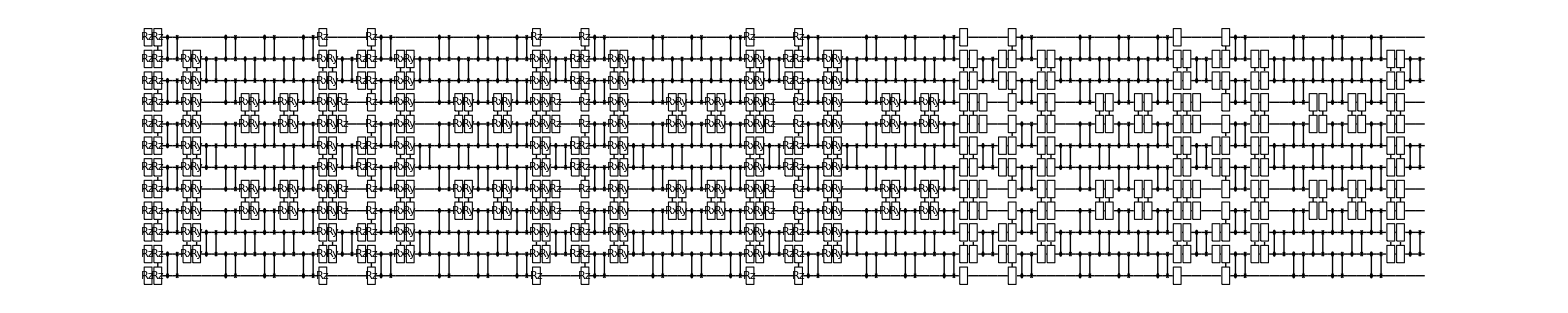

```mathematica
Subscript[Fswap, a_,b_]:={Subscript[C, a][Subscript[Z, b]],Subscript[SWAP, a,b]}
Subscript[Rep, a_,b_]:= {R[-#, Subscript[Z, a]],R[-#, Subscript[Z, b]],R[#, Subscript[Z, a] Subscript[Z, b]]}&
Subscript[Hop, a_,b_]:={ R[#, Subscript[X, a] Subscript[X, b]], R[#, Subscript[Y, a] Subscript[Y, b]]}&

swapBtwSpinLayer = Table[Subscript[Fswap, i[[1]], i[[2]]], {i, sitePairs}];
swapWthSpinLayer = Table[Subscript[Fswap, i[[1]], i[[2]]], {i, spinNoEdgePairs}];
repLayer = Table[Subscript[Rep, i[[1]], i[[2]]], {i, sitePairs}];
allHopLayer = Table[Subscript[Hop, i[[1]], i[[2]]], {i, spinPairs}];
edgeHopLayer = Table[Subscript[Hop, i[[1]], i[[2]]], {i, edgePairs}];

circuitList = {};
gateBtwSpin = 0;
gateWthSpin = 0;
paramCount=0;
Do[
	newParamCount = paramCount + Length[repLayer] -1;
	AppendTo[circuitList, MapThread[#1[#2]&, {repLayer , Table[Subscript[θ, n],{n,paramCount, newParamCount}]}]];
	paramCount = newParamCount +1;
	AppendTo[circuitList, swapBtwSpinLayer];
	gateBtwSpin = gateBtwSpin + Length[repLayer] + Length[swapBtwSpinLayer];
	

	newParamCount = paramCount + Length[allHopLayer] -1;
	AppendTo[circuitList, MapThread[#1[#2]&, {allHopLayer, Table[Subscript[θ, n],{n,paramCount, newParamCount}]}]];
	allHopParamRange= {paramCount,newParamCount};
	paramCount = newParamCount +1;
	AppendTo[circuitList, swapWthSpinLayer];
	gateWthSpin = gateWthSpin + Length[allHopLayer] + Length[swapWthSpinLayer];

	Do[
		AppendTo[circuitList, swapBtwSpinLayer];
		gateBtwSpin = gateBtwSpin + Length[swapBtwSpinLayer];
		
		If[Mod[i, 2]==1,
			newParamCount = paramCount + Length[edgeHopLayer] -1;
			AppendTo[circuitList, MapThread[#1[#2]&, {edgeHopLayer, Table[Subscript[θ, n],{n,paramCount, newParamCount}]}]];
			lastParamRange={paramCount,newParamCount};
			paramCount = newParamCount +1,
		AppendTo[circuitList, MapThread[#1[#2]&, {edgeHopLayer, Table[Subscript[θ, n],{n,lastParamRange[[1]],lastParamRange[[2]]}]}]];
			];
		AppendTo[circuitList, swapWthSpinLayer];
		gateWthSpin = gateWthSpin + Length[edgeHopLayer] + Length[swapWthSpinLayer]
	,{i,2 * ncols - 2}];

	AppendTo[circuitList, swapBtwSpinLayer];
	gateBtwSpin = gateBtwSpin + Length[swapBtwSpinLayer];

	AppendTo[circuitList, MapThread[#1[#2]&, {allHopLayer, Table[Subscript[θ, n],{n,allHopParamRange[[1]], allHopParamRange[[2]]}]}]];
	AppendTo[circuitList, swapWthSpinLayer];
	gateWthSpin = gateWthSpin + Length[allHopLayer] + Length[swapWthSpinLayer]
,nblocks]
DrawCircuit[Flatten[circuitList],nqubits]
componentList = Flatten[circuitList,1];

Assert[paramCount == nParams, "the estimated number of parameters from the structure of ansatz, should be the same as the number of parameters added during the generation of the ansatz"]
Assert[Length[componentList] == nComponents]
```

## Noisy Expectation Value Module

```mathematica
(*Calculate and save error free state, Calculate the fidelity
*)
CalcTraceDistance[qureg1_, qureg2_] := Total[Abs[SingularValueList[GetQuregMatrix[qureg1] - GetQuregMatrix[qureg2]]]]/2

NoisyExpectationValue[ paramLabel_,circErrRate_,noiseName_,hTotThreshold_:0.1,reRun_:False]:=
Module[{paramFileName,params, header,startTime,resultFile,ψ0,ψ,workspace,initCirc, resultList,resultFileName,errCircuitList,expecList,bstExpecList,ExpecList,OExpecList,GExpec,GExpecForDiffSym,GOExpecListForDiffSym, GOExpecList,GammaExpec ,symOp,hTotExpec,bstHTotExpec,HTotExpec,noiHTotExpec,resultRow, perfectFileName, densityMatrixFileName, perfectRow,perfectFile, mat,gateErrRate,detErrList,Noise,AttachNoise,GRhoInner,bstFid,Fid,noiFid ,GRhoInnerForDiffSym, symCombList,symCombName,symComb,bitErrList,p},

paramFileName = "param-"<>ToString[paramLabel]<>".csv";
If[FileExistsQ[paramFileName],

	Print["Loading param-",ToString[paramLabel]];
	params = Import[paramFileName,"List"],
	
	params = RandomReal[{0, 2Pi}, nParams];
	Print["Generated new param-",ToString[paramLabel]];
	Export[paramFileName,params,"List"]
];


perfectFileName = "param-"<>ToString[paramLabel]<>"_perfect.csv";
workspace = CreateDensityQureg[nqubits];
initCirc = Table[Subscript[X, i],{i, 0,nelectrons -1}];

If[Not[FileExistsQ[perfectFileName]], 
	
	Print["Obatining the perfect result"];
	ψ0 = CreateDensityQureg[nqubits];
	InitZeroState[ψ0];
	ApplyCircuit[initCirc,ψ0];
	ApplyCircuit[Flatten[componentList] /.Thread[ paramsSymbolList->params], ψ0];
	
	expecList =Table[CalcExpecPauliSum[ψ0, Op,workspace],{Op, pauliOpList}];
	hTotExpec = Total[pauliCoeffList * expecList];
	perfectRow = Join[{1,0, hTotExpec}, expecList];
	perfectFile=OpenWrite[perfectFileName];
	WriteString[perfectFile,ExportString[{Join[{"cost","1-Fid", "hTot"} ,pauliNameList],perfectRow},"CSV"]];
	Close[perfectFile];
	If [Abs[hTotExpec]≤ hTotThreshold, Print["Noise-free energy ", hTotExpec," is too small, move on to the next parameter"];DestroyAllQuregs[];Return[0,Module]],
	
	Print["Loading the perfect result"];
	perfectRow = Import[perfectFileName,"CSV"][[2]];
	hTotExpec = perfectRow[[3]];
	If [Abs[hTotExpec]≤ hTotThreshold, Print["Noise-free energy ", hTotExpec," is too small, move on to the next parameter"];DestroyAllQuregs[];Return[0,Module]];
	expecList  =perfectRow[[4;;]];
	
	ψ0 = CreateDensityQureg[nqubits];
	InitZeroState[ψ0];
	ApplyCircuit[initCirc,ψ0];
	ApplyCircuit[Flatten[componentList] /.Thread[ paramsSymbolList->params], ψ0];

];

gateErrRate = circErrRate / nComponents ;
detErrList = Join[{Sqrt[1-gateErrRate] IdentityMatrix[4]},Sqrt[gateErrRate/8]Map[CalcCircuitMatrix[#,2]&, {{Subscript[X, 0]},{Subscript[X, 1]}, {Subscript[Y, 0]},{Subscript[Y, 1]} ,{Subscript[X, 0],Subscript[Z, 1]},{Subscript[Z, 0],Subscript[X, 1]}, {Subscript[Y, 0],Subscript[Z, 1]},{Subscript[Z, 0],Subscript[Y, 1]}}]];
p = 1-Sqrt[1-gateErrRate];
Print[p];
bitErrList = {(1-p) IdentityMatrix[4],Sqrt[p(1-p)]CalcCircuitMatrix[{Subscript[X, 0]},2],Sqrt[p(1-p)]CalcCircuitMatrix[{Subscript[X, 1]},2], p CalcCircuitMatrix[{Subscript[X, 0],Subscript[X, 1]},2]};
Switch[noiseName, 
"Damp",Subscript[Noise, a_,b_]:= {Subscript[Damp, a][gateErrRate ], Subscript[Damp, b][gateErrRate]},
"Depol", Subscript[Noise, a_,b_]:= {Subscript[Depol, a,b][ gateErrRate]},
"Deph", Subscript[Noise, a_,b_]:= {Subscript[Deph, a,b][gateErrRate]},
"Detect",Subscript[Noise, a_,b_]:= {Subscript[Kraus, a,b][detErrList] },
"Bit",Subscript[Noise, a_,b_]:= {Subscript[Kraus, a,b][bitErrList] }];
AttachNoise = ReplaceAll[{Subscript[Fswap, a_,b_]:>Join[Subscript[Fswap, a,b], Subscript[Noise, a,b]],Subscript[Rep, a_,b_][Subscript[θ, n_]]:>Join[Subscript[Rep, a,b][Subscript[θ, n]], Subscript[Noise, a,b]],Subscript[Hop, a_,b_][Subscript[θ, n_]]:>Join[Subscript[Hop, a,b][Subscript[θ, n]], Subscript[Noise, a,b]]}];
errCircuitList = Flatten[AttachNoise[circuitList]];




Print["Performing simulation with the circuit error rate ", circErrRate];
resultFileName = "param-"<>ToString[paramLabel]<>"_nCircErr-"<>ToString[circErrRate]<>"_"<>noiseName<>".csv";
(*header = Join[{"","cost","1-Pur","1-Fid","TrDist","SqrtHSDist", "hTotDiff","hTot"} ,pauliNameList];*)
header = Join[{"","cost","1-Fid", "hTotDiff","hTot"} ,pauliNameList];

If[Not[FileExistsQ[resultFileName]] || reRun, 

	resultFile=OpenWrite[resultFileName];
	WriteString[resultFile,ExportString[{header},"CSV"]];
	Close[resultFile],
	
	Print["Calculation is already done"];
	DestroyAllQuregs[];
	Return[0,Module]
];

resultList={};
startTime=AbsoluteTime[];



Print["Obatining the Noisy result"];
ψ = CreateDensityQureg[nqubits];
InitZeroState[ψ];
ApplyCircuit[initCirc,ψ];

ApplyCircuit[errCircuitList/.Thread[ paramsSymbolList->params], ψ];
OExpecList =Table[CalcExpecPauliSum[ψ, Op,workspace],{Op, pauliOpList}];
noiHTotExpec = Total[pauliCoeffList * OExpecList];
(*noiPur = CalcPurity[ψ];*)
noiFid =  CalcDensityInnerProduct[ψ0,ψ];
(*noiTrDist = CalcTraceDistance[ψ0,ψ];
noiHSDist = CalcHilbertSchmidtDistance[ψ0,ψ];*)
resultRow = Join[{"Noisy",1,1-noiFid,noiHTotExpec-hTotExpec,noiHTotExpec}, OExpecList];
AppendTo[resultList, resultRow];

GExpecForDiffSym={1};
GOExpecListForDiffSym = {OExpecList};
GRhoInnerForDiffSym = {noiFid};
Do[symOp = symOpList[[i]];
	Print["Obtaining Boost Results for " <> symNameList[[i]]];
	GExpec =CalcExpecPauliSum[ψ, symOp,workspace] ;
	ApplyPauliSum[ψ,symOp/GExpec,workspace ];
	bstFid = CalcDensityInnerProduct[ψ0,workspace];
	GOExpecList =Table[CalcExpecPauliSum[ψ, PauliProd[Op,symOp],workspace],{Op, pauliOpList}];
	
	GRhoInner = bstFid * GExpec;
	bstExpecList =GOExpecList/GExpec ;
	bstHTotExpec = Total[pauliCoeffList * bstExpecList];
	
	resultRow = Join[{symNameList[[i]]<>"Bst",1/GExpec^2,1-bstFid,bstHTotExpec-hTotExpec,bstHTotExpec}, bstExpecList];
	AppendTo[GExpecForDiffSym, GExpec];
	AppendTo[GRhoInnerForDiffSym, GRhoInner];
	AppendTo[GOExpecListForDiffSym, GOExpecList];
	AppendTo[resultList, resultRow];

,{i,Length[symOpList]}];

symCombList =  {{1,2}, {1,3}, {1,4},{2,3},{2,4}, {3,4}, {1,2,3,4}};
symCombName = {"UpVer", "DnVer","TotVer","UpBst+FullVer", "UpBst+DnVer","DnBst+UpVer", "FullVer"};
Do[symComb = symCombList[[i]];
	(*Print["Obtaining Results for " <>symCombName [[i]]];*)
	GammaExpec = Total[GExpecForDiffSym[[symComb]]]/Length[symComb];

	Fid =Total[GRhoInnerForDiffSym[[symComb]]]/(Length[symComb]*GammaExpec) ;
	ExpecList =Total[GOExpecListForDiffSym [[symComb]] ]/(Length[symComb]*GammaExpec) ;
	HTotExpec = Total[pauliCoeffList * ExpecList];


	resultRow = Join[{symCombName [[i]],1/GammaExpec^2,1-Fid,HTotExpec-hTotExpec,HTotExpec}, ExpecList];
	AppendTo[resultList, resultRow];
,{i,Length[symCombList]}];

resultFile=OpenAppend[resultFileName];
WriteString[resultFile,ExportString[resultList,"CSV"]];
Close[resultFile];
DestroyAllQuregs[]
]
```

## Run Module

```mathematica
startTime = AbsoluteTime[];
Do[NoisyExpectationValue[paramLabel,circErrRate,noiseName,energyThreshold, True],{paramLabel,paramLabelList},{circErrRate, circErrRateList}]
Print["We have used ", AbsoluteTime[] - startTime, "s."]
```

Loading param-1

Loading the perfect result

0.000347283

Performing simulation with the circuit error rate 0.1

Obatining the Noisy result

Obtaining Boost Results for Up

Obtaining Boost Results for Dn

Obtaining Boost Results for Tot

Loading param-1

Loading the perfect result

0.000694686

Performing simulation with the circuit error rate 0.2

Obatining the Noisy result

Obtaining Boost Results for Up

Obtaining Boost Results for Dn

Obtaining Boost Results for Tot

Loading param-1

Loading the perfect result

0.00104221

Performing simulation with the circuit error rate 0.3

Obatining the Noisy result

Obtaining Boost Results for Up

Obtaining Boost Results for Dn

Obtaining Boost Results for Tot

Loading param-1

Loading the perfect result

0.00138985

Performing simulation with the circuit error rate 0.4

Obatining the Noisy result

Obtaining Boost Results for Up

Obtaining Boost Results for Dn

Obtaining Boost Results for Tot

Loading param-1

Loading the perfect result

0.00173762

Performing simulation with the circuit error rate 0.5

Obatining the Noisy result

Obtaining Boost Results for Up

Obtaining Boost Results for Dn

Obtaining Boost Results for Tot

We have used 6.34601s.